```mathematica
<<"/home/iubuntu/Descargas/github/caso1/RRT/RandomData.m"
```

```mathematica
lambda=100;
mu=100;
ro=0.6;
nmax=10000;
```

Apartado 2

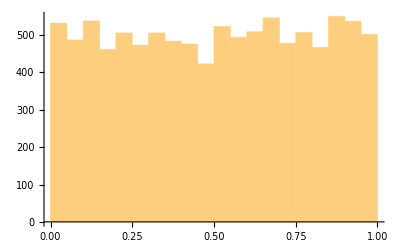

```mathematica
histuniform= Table[RandomData[],nmax];
Histogram[histuniform]
```

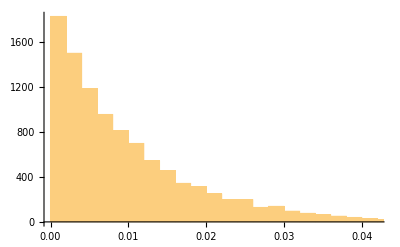

```mathematica
InterArr= Table[RandomExp[lambda],nmax];
Histogram[InterArr]
```

Apartado 3

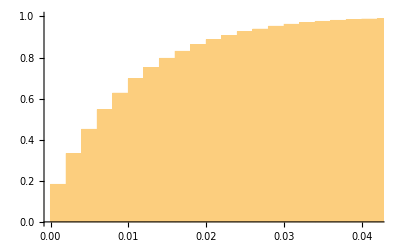

```mathematica
Histogram[InterArr, 50,"CDF"]
```

# PARTE 2

Apartado 4

Para hacer funciones: P.ej, acumular arrivals (sumar una con la anterior)

```mathematica
Arriv=Accumulate[InterArr];
```

```mathematica
ServiceTime=Table[RandomExp[mu],nmax];
```

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
DeparturesTime=FifoSchedulling[Arriv,ServiceTime];
```

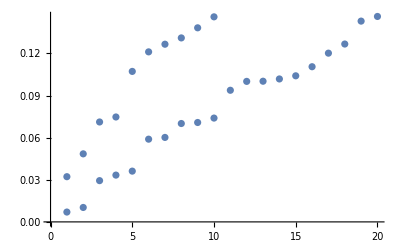

```mathematica
Show[ListPlot[Arriv[[1;;20]]],ListPlot[DeparturesTime[[1;;20]]]]
```

```mathematica
Manipulate[ListPlot[{Arriv[[origin;;origin+width]],DeparturesTime[[origin;;origin+width]]}],{origin,1,1000-width,1},{width,10,40,1}]
```

Funcion que se ha inventado para hacer la escalera:

```mathematica
PointStair[lst_]:=Module[{n=0,lastTime=0},Flatten[Map[({{lastTime,n},{lastTime=#,n++}})&,lst],1]]
```

```mathematica
Manipulate[ListLinePlot[{PointStair[Arriv[[1;;width]]],PointStair[DeparturesTime[[1;;width]]]}],{width,10,40,1}]
```

Otra opcion (usando funcion del Mathematica)

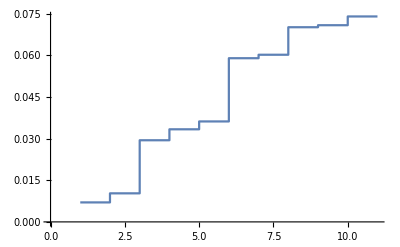

```mathematica
ListStepPlot[Arriv[[1;;10]]]
```

Para montañas (Numero de usuarios en el sistema)

```mathematica
ArrivalsEvent[lst_]:=Map[{#,1}&,lst];
```

```mathematica
DepartureEvents[lst_]:=Map[{#,-1}&,lst];
```

```mathematica
DrawMontain[lst_]:=Module[{n=0,lastTime=0},
Flatten[
Map[{{lastTime,n},{lastTime=#[[1]],
If[#[[2]]==1,n++,n--]}}&,
lst],
1
]]
```

```mathematica
EventList=Sort[Join[ArrivalsEvent[Arriv[[]]],DepartureEvents[DeparturesTime[[]]]]];
```

```mathematica
listStat=DrawMontain[EventList];
```

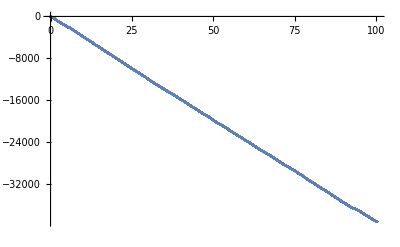

```mathematica
ListLinePlot[DrawMontain[listStat]]
```

```mathematica
Manipulate[
ListLinePlot[listStat[[1;;width]]],
{width,10,100,1}]
```

Apartado 5

DetparureTime - ArrivalsTime acumulado y dividido entre el nudm e arrivals y todo eso en funcion de ro (divicios entre landa y mu)

```mathematica
GetMeanTime[ArrivalTimes_,DepartureTimes_]:=Module[{acum,i},For[i=0,i<Length[ArrivalTimes],i++;
	acum+=DepartureTimes[[i]]-ArrivalTimes[[i]];];Return[acum/Length[ArrivalTimes]]]
```

```mathematica
MeanTimeOfRo[lambda_,mu_,n_]:=Module[{ro=lambda/mu,i,acum},Table[i,{i,0,n,1}];
For[i=1,i<n,InterArrTime=Table[RandomExp[lambda],n];
Arriv=Accumulate[InterArrTime];
ServiceTime=Table[RandomExp[mu],n];
DeparturesTime=FifoSchedulling[Arriv,ServiceTime];
acum[[i]]=GetMeanTime[Arriv,DeparturesTime];]Return[acum]];
```

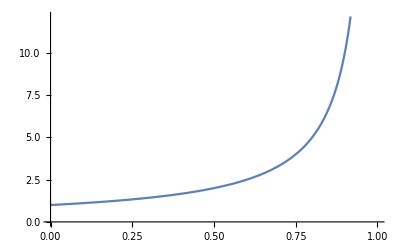

```mathematica
teoric=Plot[1/(1-ro),{ro,0,1},AxesOrigin->{0,0},MeanTimeOfRo[lambda,mu,ro]];
```

Apartado 6

```mathematica
GetStat[lst_,stat_]:=Module[{time=0,lastTime=0},Map[(If[#[[2]]==stat,time+=#[[1]]-lastTime];
lastTime=#[[1]])&,lst];time]
```

```mathematica
ProbTotal[lst_,numest_]:=Module[{estados=Table[i,{i,0,numest,1}]},Map[(GetStat[lst,#]/(lst[[Length[lst]]][[1]]-lst[[1]][[1]]))&,estados]]
```

```mathematica
CheckProb[probs_]:=Module[{acum=0},Map[(acum+=#)&,probs];acum]
```

```mathematica
probabilities=ProbTotal[listStat,8];
CheckProb[probabilities]
```

0.12665

Otra funcion que me he montado pero que no funciona aun

ObtainMaxUserConnected[lst_] := 
 Module[{maxValue = 0},
  Map[(If[#[lst[[]]]])];
  maxValue]

ObtainMaxUserConnected[listStat];